```mathematica
Equations from arXiv : 1803.01944, data file from the attached code repository
```

```mathematica
POMS[f_]:= (1.5*10^-11 )^2(1+((2*10^-3)/f)^4)
```

```mathematica
PACC[f_]:= (3*10^-15)^2(1+((.4*10^-3)/f)^2)(1+(f/(8*10^-3))^4)
```

```mathematica
L = 2.5*10^9;
fstar = 19.09*10^-3;
```

```mathematica
rdat = Import["../data/LISA_Rfunction.txt","Table"];
```

Import::nffil: File not found during Import.

```mathematica
rdat = Import["/Users/sperkins/opt/gw_analysis_tools/data/LISA_Rfunction.txt","Table"];
```

```mathematica
gwatSn = Import["/Users/sperkins/Shared/Research/population_studies/current_efforts/data/LISA_SN.csv","Table"];
gwatf = Import["/Users/sperkins/Shared/Research/population_studies/current_efforts/data/WF_f.csv","Table"];
```

```mathematica
gwatdata = Table[{gwatf[[i]][[1]],(gwatSn[[i]][[1]])^(.5)},{i,1,Length[gwatSn]}];
```

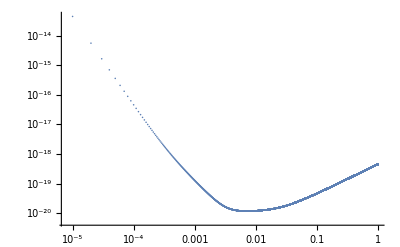

```mathematica
ListLogLogPlot[gwatdata]
```

```mathematica
gwatSn[[1]]
```

{1.97249×10^-27}

```mathematica
rdat = rdat/.{x_,y_}->{x*fstar,y};(*Rescale the file*)
```

```mathematica
R= Interpolation[rdat]
```

InterpolatingFunction[…]

```mathematica
S1[f_]:=10/(3 L^2)(POMS[f] + 2(1+Cos[f/fstar]^2)PACC[f]/(2π f)^4)(1 + 6/10(f/fstar)^2);
S2[f_]:=1/(2 L^2)(POMS[f] + 2(1+Cos[f/fstar]^2)PACC[f]/(2π f)^4)/R[f];
```

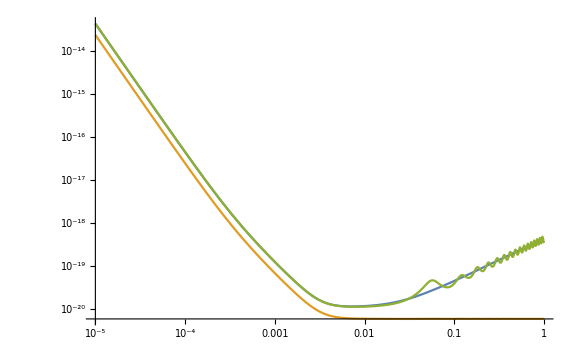

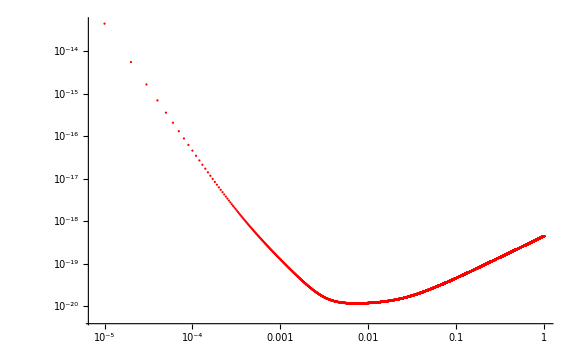

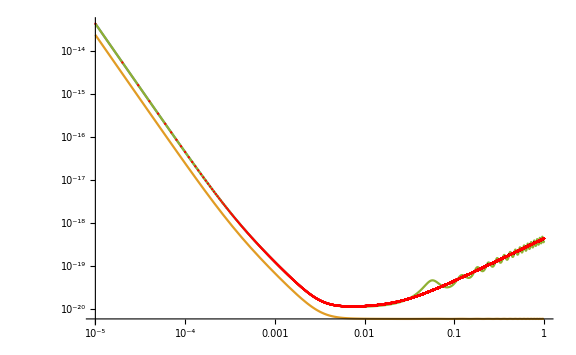

```mathematica
plot1=LogLogPlot[{S1[f]^(.5),√(1/L^2(POMS[f] + 2(1+Cos[f/fstar]^2)PACC[f]/(2π f)^4)),S2[f]^(.5)},{f,10^-5,10^0},ImageSize->Large]
plot2 = ListLogLogPlot[gwatdata,PlotStyle->{Red}]
Show[plot1,plot2]
```

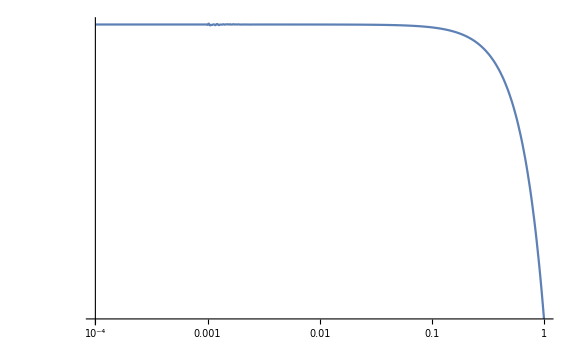

```mathematica
LogLogPlot[R[f],{f,10^-4,1},ImageSize->Large,PlotRange->Full]
```

```mathematica
dat = Table[{Log[f],Log[R[f]]},{f,10^-5,1,.00001}]
```

{{-11.5129,-1.89712},{-10.8198,-1.89712},{-10.4143,-1.89712},{-10.1266,-1.89712},99992,{-0.0000300005,-2.24208},{-0.0000200002,-2.24209},{-0.0000100001,-2.24209},{0.,-2.2421}}
 |  |  |  |

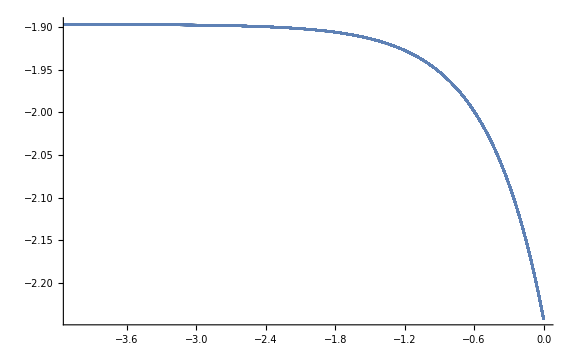

```mathematica
ListPlot[dat,ImageSize->Large]
```